# Úkol 1: Výpočetní složitost

Jméno a příjmení:  Martin Krčma

## Zadání:

Naprogramovat 4 různé řadící algoritmy.
	alespoň 2x O(n*log(n))
	můžete využít algoritmy naprogramované společně na cvičení (Bubble Sort a Quick Sort)
Ověřit čas potřebný pro seřazení pole stejných náhodných čísel o rozměru 10, 100,1000,10000,100000 prvků.
Ověřit čas potřebný pro seřazení seřazeného pole čísel o velikosti 10, 100,1000,10000,100000 prvků.
Ověřit čas potřebný pro seřazení obráceně seřazeného pole čísel o velikosti 10, 100,1000,10000,100000 prvků.
Každé měření by mělo být opakováno nejmíně 11x a zaznamenán aritmetický průměr času potřebného k seřazení.
Porovnat teoretickou složitost algoritmů s naměřenými výsledky pomocí tabulek a grafů.
Srovnejte naměřené časy s vestavěnou funkcí Sort[].
Výsledný report bude obsahovat slovní závěr, ve kterém zodpovíte následující otázky:
	Jaký třídící algoritmus byl nejrychlejší?
	Mají nějakou výhodu algoritmy s časovou složitostí O(n^2) ? Proč se používají?

## Třidící algoritmy:

## Quick sort

```mathematica
quickSort[x_]:=Module[{y=x,pivot,A,B,C,i},
If[Length@y≤1,Return@y];
pivot=RandomInteger[{1,Length@y}];
A={};
B={y[[pivot]]};
C={};
For[i=1,i≤Length@y,i++,If[i==pivot,Continue[]];
If[y[[i]]>y[[pivot]],AppendTo[A,y[[i]]];,AppendTo[C,y[[i]]];];];
A=quickSort@A;
C=quickSort@C;
Return[Join[A,B,C]];
];
```

## Merge sort

```mathematica
merge[ar_, ax_, left_, right_] := Module[{arr = ar, aux = ax, middle = Floor [(left + right)/2], leftI,  rightI, auxI},
leftI = left;
rightI = middle + 1;
auxI = left;
While[leftI ≤ middle && rightI ≤ right, { 
If[arr[[leftI]] ≥ arr[[rightI]], 
aux[[auxI]] = arr[[leftI++]],
aux[[auxI]] = arr[[rightI++]]
];
auxI++;
}];
While[leftI ≤ middle, 
aux[[auxI++]] = arr[[leftI++]];
];
While[rightI ≤ right,
aux[[auxI++]] = arr[[rightI++]];
];
Return@{arr, aux};
];
mergeSort[ar_, ax_, left_, right_] := Module[{arr = ar, aux = ax, middle, i},
If[left == right, Return@{arr, aux}];
middle = Floor[(left + right)/2];
{arr, aux} = mergeSort[arr, aux, left, middle];
{arr, aux} = mergeSort[arr, aux, middle + 1, right];
{arr, aux} = merge[arr, aux, left, right];
For[i = left,i ≤ right, i++, 
arr[[i]] = aux[[i]]
];
Return@{arr, aux};
];
```

## Shell sort

```mathematica
shellSort[ar_]:=Module[{arr=ar,interval=0, outer,valToInsert,inner},
While[interval<Floor[Length@arr/3],
interval=interval*3+1;
];
While[interval>0,
For[outer=interval,outer<=Length@arr,outer++,
valToInsert=arr[[outer]];
inner=outer;
While[inner>interval-1&&arr[[inner-interval]]≥valToInsert,
arr[[inner]]=arr[[inner-interval]];
inner=inner-interval;
];
arr[[inner]]=valToInsert;
];
interval=Floor[(interval-1)/3];
];
Return@arr;
];
```

## Counting sort

```mathematica
countingSort[ar_] := Module[{arr = ar, aux, min, max, i,counts},
aux = Table[0, Length@arr];
min = arr[[1]];
max = arr[[1]];
For[i = 2,i≤Length@arr,i++,
If[arr[[i]]<min,
min = arr[[i]],
If[arr[[i]]>max,max = arr[[i]]];
];
];
counts = Table[0, max - min +1];
For[i = 1,i≤ Length@arr,i++,
counts[[arr[[i]] - min + 1]]++;
];
counts[[1]]--;
For[i = 2,i≤ Length@counts,i++,
counts[[i]]=counts[[i]]+counts[[i-1]];
];
For[i = Length@arr,i > 0,i--,
aux[[1 + counts[[arr[[i]]-min + 1]]--]]=arr[[i]];
];
Return@aux;
];
```

## Čas potřebný pro seřazení pole

## Pole nahodných čisel

```mathematica
p10 = RandomInteger[{0,1000},10];
p100 = RandomInteger[{0,1000},100];
p1000= RandomInteger[{0,1000},1000];
p10000 = RandomInteger[{0,1000},10000];
p100000 = RandomInteger[{0,1000},100000];
```

Quick sort

```mathematica
quickSort10 = Mean[Table[AbsoluteTiming[quickSort[p10]][[1]], 11]];
quickSort100 = Mean[Table[AbsoluteTiming[quickSort[p100]][[1]], 11]];
quickSort1000 = Mean[Table[AbsoluteTiming[quickSort[p1000]][[1]], 11]];
quickSort10000 = Mean[Table[AbsoluteTiming[quickSort[p10000]][[1]], 11]];
quickSort100000 = Mean[Table[AbsoluteTiming[quickSort[p100000]][[1]], 11]];
```

Merge sort

```mathematica
mergeSort10 = Mean[Table[AbsoluteTiming[mergeSort[p10, p10,1,10]][[1]], 11]];
mergeSort100 = Mean[Table[AbsoluteTiming[mergeSort[p100, p100, 1, 100]][[1]], 11]];
mergeSort1000 = Mean[Table[AbsoluteTiming[mergeSort[p1000, p1000, 1, 1000]][[1]], 11]];
mergeSort10000 = Mean[Table[AbsoluteTiming[mergeSort[p10000, p10000, 1, 10000]][[1]], 11]];
mergeSort100000 = Mean[Table[AbsoluteTiming[mergeSort[p100000, p100000, 1, 100000]][[1]], 11]];
```

Shell sort

```mathematica
shellSort10 = Mean[Table[AbsoluteTiming[shellSort[p10]][[1]], 11]];
shellSort100 = Mean[Table[AbsoluteTiming[shellSort[p100]][[1]], 11]];
shellSort1000 = Mean[Table[AbsoluteTiming[shellSort[p1000]][[1]], 11]];
shellSort10000 = Mean[Table[AbsoluteTiming[shellSort[p10000]][[1]], 11]];
shellSort100000 = Mean[Table[AbsoluteTiming[shellSort[p100000]][[1]], 11]];
```

Counting sort

```mathematica
countingSort10 = Mean[Table[AbsoluteTiming[countingSort[p10]][[1]], 11]];
countingSort100 = Mean[Table[AbsoluteTiming[countingSort[p100]][[1]], 11]];
countingSort1000 = Mean[Table[AbsoluteTiming[countingSort[p1000]][[1]], 11]];
countingSort10000 = Mean[Table[AbsoluteTiming[countingSort[p10000]][[1]], 11]];
countingSort100000 = Mean[Table[AbsoluteTiming[countingSort[p100000]][[1]], 11]];
```

Wolfram sort

```mathematica
sort10 = Mean[Table[AbsoluteTiming[Sort[p10]][[1]], 11]];
sort100 = Mean[Table[AbsoluteTiming[Sort[p100]][[1]], 11]];
sort1000 = Mean[Table[AbsoluteTiming[Sort[p1000]][[1]], 11]];
sort10000 = Mean[Table[AbsoluteTiming[Sort[p10000]][[1]], 11]];
sort100000 = Mean[Table[AbsoluteTiming[Sort[p100000]][[1]], 11]];
```

Vypočet teoretické složitosti algoritmu

```mathematica
k1 = quickSort1000/(1000*Log[1000]);
quickSort10T = 10*Log[10]*k1;
quickSort100T = 100*Log[100]*k1;
quickSort1000T = 1000*Log[1000]*k1;
quickSort10000T = 10000*Log[10000]*k1;
quickSort100000T = 100000*Log[100000]*k1;
```

```mathematica
k2 = mergeSort1000/(1000*Log[1000]);
mergeSort10T = 10*Log[10]*k2;
mergeSort100T = 100*Log[100]*k2;
mergeSort1000T = 1000*Log[1000]*k2;
mergeSort10000T = 10000*Log[10000]*k2;
mergeSort100000T = 100000*Log[100000]*k2;
```

```mathematica
k3 = shellSort1000/1000^(4/3);
shellSort10T = 10^(4/3)*k3;
shellSort100T = 100^(4/3)*k3;
shellSort1000T = 1000^(4/3)*k3;
shellSort10000T = 10000^(4/3)*k3;
shellSort100000T = 100000^(4/3)*k3;
```

```mathematica
k4 = countingSort1000/(1000+CountDistinct@p1000);
countingSort10T = (10+CountDistinct@p1000)*k4;
countingSort100T = (100+CountDistinct@p1000)*k4;
countingSort1000T = (1000+CountDistinct@p1000)*k4;
countingSort10000T = (10000+CountDistinct@p1000)*k4;
countingSort100000T = (100000+CountDistinct@p1000)*k4;
```

Porovnaní hodnot

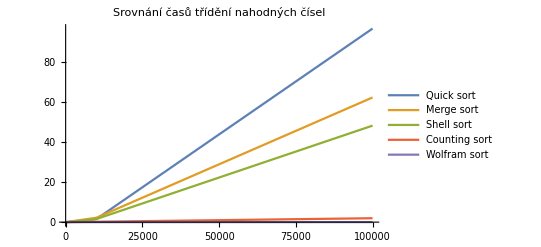

```mathematica
ListPlot[{
	{{10,quickSort10}, {100, quickSort100}, {1000, quickSort1000}, {10000, quickSort10000}, {100000, quickSort100000}},
	{{10,mergeSort10}, {100, mergeSort100}, {1000, mergeSort1000}, {10000, mergeSort10000}, {100000, mergeSort100000}},
	{{10,shellSort10}, {100, shellSort100}, {1000, shellSort1000}, {10000, shellSort10000}, {100000, shellSort100000}},
	{{10,countingSort10}, {100, countingSort100}, {1000, countingSort1000}, {10000, countingSort10000}, {100000, countingSort100000}},
	{{10,sort10}, {100, sort100}, {1000, sort1000}, {10000, sort10000}, {100000, sort100000}}
},
Joined->True,
PlotLegends->{"Quick sort", "Merge sort", "Shell sort", "Counting sort", "Wolfram sort"},
PlotLabel->"Srovnání časů třídění nahodných čísel",
PlotRange->All
]
```

```mathematica
Grid[{
{"n", "Quick sort", "Quick sort (T)", "Merge sort", "Merge sort (T)", "Shell sort", "Shell sort (T)", "Counting sort", "Counting sort (T)","Wolfram sort"},
{10, quickSort10, quickSort10T,mergeSort10,mergeSort10T,shellSortt10,shellSort10T,countingSort10,countingSort10T,sort10},
{100, quickSort100, quickSort100T,mergeSort100,mergeSort100T,shellSort100,shellSort100T,countingSort100,countingSort100T,sort100},
{1000, quickSort1000, quickSort1000T,mergeSort1000,mergeSort1000T,shellSort1000,shellSort1000T,countingSort1000,countingSort1000T,sort1000},
{10000, quickSort10000, quickSort10000T,mergeSort10000,mergeSort10000T,shellSort10000,shellSort10000T,countingSort10000,countingSort10000T,sort10000},
{100000, quickSort100000, quickSort100000T,mergeSort100000,mergeSort100000T,shellSort100000,shellSort100000T,countingSort100000,countingSort100000T,sort100000}
}, Frame->All
]
```

n | Quick sort | Quick sort (T) | Merge sort | Merge sort (T) | Shell sort | Shell sort (T) | Counting sort | Counting sort (T) | Wolfram sort
10 | 0.000982355 | 0.000255759 | 0.000936018 | 0.000700066 | 0.000158 | 0.000140961 | 0.00444857 | 0.00731753 | 3.8×10^-6
100 | 0.00516707 | 0.00511518 | 0.00892921 | 0.0140013 | 0.00466482 | 0.0030369 | 0.00391334 | 0.00839364 | 7.89091×10^-6
1000 | 0.0767277 | 0.0767277 | 0.21002 | 0.21002 | 0.0654281 | 0.0654281 | 0.0191547 | 0.0191547 | 0.0000715273
10000 | 1.53519 | 1.02304 | 2.19227 | 2.80026 | 1.5498 | 1.40961 | 0.19886 | 0.126765 | 0.000957709
100000 | 97.0006 | 12.7879 | 62.4745 | 35.0033 | 48.3648 | 30.369 | 1.9615 | 1.20287 | 0.0114368

## Seřazené pole

```mathematica
ps10 = Sort@p10;
ps100 = Sort@p100;
ps1000 = Sort@p1000;
ps10000 = Sort@p10000;
ps100000 = Sort@p100000;
```

Quick sort

```mathematica
quickSort10s = Mean[Table[AbsoluteTiming[quickSort[ps10]][[1]], 11]];
quickSort100s = Mean[Table[AbsoluteTiming[quickSort[ps100]][[1]], 11]];
quickSort1000s = Mean[Table[AbsoluteTiming[quickSort[ps1000]][[1]], 11]];
quickSort10000s = Mean[Table[AbsoluteTiming[quickSort[ps10000]][[1]], 11]];
quickSort100000s = Mean[Table[AbsoluteTiming[quickSort[ps100000]][[1]], 11]];
```

Merge sort

```mathematica
mergeSort10s = Mean[Table[AbsoluteTiming[mergeSort[ps10, ps10,1,10]][[1]], 11]];
mergeSort100s = Mean[Table[AbsoluteTiming[mergeSort[ps100, ps100, 1, 100]][[1]], 11]];
mergeSort1000s = Mean[Table[AbsoluteTiming[mergeSort[ps1000, ps1000, 1, 1000]][[1]], 11]];
mergeSort10000s = Mean[Table[AbsoluteTiming[mergeSort[ps10000, ps10000, 1, 10000]][[1]], 11]];
mergeSort100000s = Mean[Table[AbsoluteTiming[mergeSort[ps100000, ps100000, 1, 100000]][[1]], 11]];
```

Shell sort

```mathematica
shellSort10s = Mean[Table[AbsoluteTiming[shellSort[ps10]][[1]], 11]];
shellSort100s = Mean[Table[AbsoluteTiming[shellSort[ps100]][[1]], 11]];
shellSort1000s = Mean[Table[AbsoluteTiming[shellSort[ps1000]][[1]], 11]];
shellSort10000s = Mean[Table[AbsoluteTiming[shellSort[ps10000]][[1]], 11]];
shellSort100000s = Mean[Table[AbsoluteTiming[shellSort[ps100000]][[1]], 11]];
```

Counting sort

```mathematica
countingSort10s = Mean[Table[AbsoluteTiming[countingSort[ps10]][[1]], 11]];
countingSort100s = Mean[Table[AbsoluteTiming[countingSort[ps100]][[1]], 11]];
countingSort1000s = Mean[Table[AbsoluteTiming[countingSort[ps1000]][[1]], 11]];
countingSort10000s = Mean[Table[AbsoluteTiming[countingSort[ps10000]][[1]], 11]];
countingSort100000s = Mean[Table[AbsoluteTiming[countingSort[ps100000]][[1]], 11]];
```

Wolfram sort

```mathematica
sort10s = Mean[Table[AbsoluteTiming[Sort[ps10]][[1]], 11]];
sort100s = Mean[Table[AbsoluteTiming[Sort[ps100]][[1]], 11]];
sort1000s = Mean[Table[AbsoluteTiming[Sort[ps1000]][[1]], 11]];
sort10000s = Mean[Table[AbsoluteTiming[Sort[ps10000]][[1]], 11]];
sort100000s = Mean[Table[AbsoluteTiming[Sort[ps100000]][[1]], 11]];
```

Vypočet teoretické složitosti algoritmu

```mathematica
k1s = quickSort1000s/(1000*Log[1000]);
quickSort10Ts = 10*Log[10]*k1s;
quickSort100Ts = 100*Log[100]*k1s;
quickSort1000Ts = 1000*Log[1000]*k1s;
quickSort10000Ts = 10000*Log[10000]*k1s;
quickSort100000Ts = 100000*Log[100000]*k1s;
```

```mathematica
k2s = mergeSort1000s/(1000*Log[1000]);
mergeSort10Ts = 10*Log[10]*k2s;
mergeSort100Ts = 100*Log[100]*k2s;
mergeSort1000Ts = 1000*Log[1000]*k2s;
mergeSort10000Ts = 10000*Log[10000]*k2s;
mergeSort100000Ts = 100000*Log[100000]*k2s;
```

```mathematica
k3s = shellSort1000s/1000^(4/3);
shellSort10Ts = 10^(4/3)*k3s;
shellSort100Ts = 100^(4/3)*k3s;
shellSort1000Ts = 1000^(4/3)*k3s;
shellSort10000Ts = 10000^(4/3)*k3s;
shellSort100000Ts = 100000^(4/3)*k3s;
```

```mathematica
k4s = countingSort1000s/(1000+CountDistinct@ps1000);
countingSort10Ts = (10+CountDistinct@p1000)*k4s;
countingSort100Ts = (100+CountDistinct@p1000)*k4s;
countingSort1000Ts = (1000+CountDistinct@p1000)*k4s;
countingSort10000Ts = (10000+CountDistinct@p1000)*k4s;
countingSort100000Ts = (100000+CountDistinct@p1000)*k4s;
```

Porovnaní hodnot

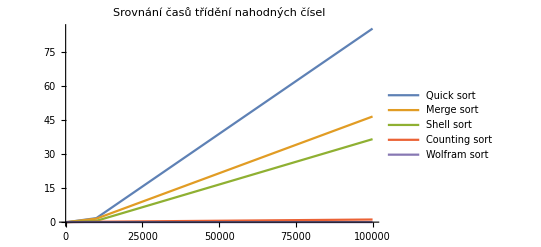

```mathematica
ListPlot[{
	{{10,quickSort10s}, {100, quickSort100s}, {1000, quickSort1000s}, {10000, quickSort10000s}, {100000, quickSort100000s}},
	{{10,mergeSort10s}, {100, mergeSort100s}, {1000, mergeSort1000s}, {10000, mergeSort10000s}, {100000, mergeSort100000s}},
	{{10,shellSort10s}, {100, shellSort100s}, {1000, shellSort1000s}, {10000, shellSort10000s}, {100000, shellSort100000s}},
	{{10,countingSort10s}, {100, countingSort100s}, {1000, countingSort1000s}, {10000, countingSort10000s}, {100000, countingSort100000s}},
	{{10,sort10s}, {100, sort100s}, {1000, sort1000s}, {10000, sort10000s}, {100000, sort100000s}}
},
Joined->True,
PlotLegends->{"Quick sort", "Merge sort", "Shell sort", "Counting sort", "Wolfram sort"},
PlotLabel->"Srovnání časů třídění nahodných čísel",
PlotRange->All
]
```

```mathematica
Grid[{
{"n", "Quick sort", "Quick sort (T)", "Merge sort", "Merge sort (T)", "Shell sort", "Shell sort (T)", "Counting sort", "Counting sort (T)","Wolfram sort"},
{10, quickSort10s, quickSort10Ts,mergeSort10s,mergeSort10Ts,shellSort10s,shellSort10Ts,countingSort10s,countingSort10Ts,sort10s},
{100, quickSort100s, quickSort100Ts,mergeSort100s,mergeSort100Ts,shellSort100s,shellSort100Ts,countingSort100s,countingSort100Ts,sort100s},
{1000, quickSort1000s, quickSort1000Ts,mergeSort1000s,mergeSort1000Ts,shellSort1000s,shellSort1000Ts,countingSort1000s,countingSort1000Ts,sort1000s},
{10000, quickSort10000s, quickSort10000Ts,mergeSort10000s,mergeSort10000Ts,shellSort10000s,shellSort10000Ts,countingSort10000s,countingSort10000Ts,sort10000s},
{100000, quickSort100000s, quickSort100000Ts,mergeSort100000s,mergeSort100000Ts,shellSort100000s,shellSort100000Ts,countingSort100000s,countingSort100000Ts,sort100000s}
}, Frame->All
]
```

n | Quick sort | Quick sort (T) | Merge sort | Merge sort (T) | Shell sort | Shell sort (T) | Counting sort | Counting sort (T) | Wolfram sort
10 | 0.000904264 | 0.000342428 | 0.000917018 | 0.000379667 | 0.0001446 | 0.0000584823 | 0.0063503 | 0.00804979 | 2.12727×10^-6
100 | 0.0057694 | 0.00684857 | 0.00986038 | 0.00759335 | 0.0028381 | 0.00125996 | 0.00801202 | 0.00923359 | 2.53636×10^-6
1000 | 0.102729 | 0.102729 | 0.1139 | 0.1139 | 0.0271451 | 0.0271451 | 0.0210715 | 0.0210715 | 0.0000108909
10000 | 1.75673 | 1.36971 | 1.52545 | 1.51867 | 0.563818 | 0.584823 | 0.174056 | 0.139451 | 0.0000824
100000 | 85.1377 | 17.1214 | 46.4607 | 18.9834 | 36.5051 | 12.5996 | 1.14979 | 1.32324 | 0.000669073

## Obracené seřazené pole

```mathematica
psr10 = Reverse@ps10;
psr100 = Reverse@ps100;
psr1000 = Reverse@ps1000;
psr10000 = Reverse@ps10000;
psr100000 = Reverse@ps100000;
```

Quick sort

```mathematica
quickSort10sr = Mean[Table[AbsoluteTiming[quickSort[psr10]][[1]], 11]];
quickSort100sr = Mean[Table[AbsoluteTiming[quickSort[psr100]][[1]], 11]];
quickSort1000sr = Mean[Table[AbsoluteTiming[quickSort[psr1000]][[1]], 11]];
quickSort10000sr = Mean[Table[AbsoluteTiming[quickSort[psr10000]][[1]], 11]];
quickSort100000sr = Mean[Table[AbsoluteTiming[quickSort[psr100000]][[1]], 11]];
```

Merge sort

```mathematica
mergeSort10sr = Mean[Table[AbsoluteTiming[mergeSort[psr10, psr10,1,10]][[1]], 11]];
mergeSort100sr = Mean[Table[AbsoluteTiming[mergeSort[psr100, psr100, 1, 100]][[1]], 11]];
mergeSort1000sr = Mean[Table[AbsoluteTiming[mergeSort[psr1000, psr1000, 1, 1000]][[1]], 11]];
mergeSort10000sr = Mean[Table[AbsoluteTiming[mergeSort[psr10000, psr10000, 1, 10000]][[1]], 11]];
mergeSort100000sr = Mean[Table[AbsoluteTiming[mergeSort[psr100000, psr100000, 1, 100000]][[1]], 11]];
```

Shell sort

```mathematica
shellSort10sr = Mean[Table[AbsoluteTiming[shellSort[psr10]][[1]], 11]];
shellSort100sr = Mean[Table[AbsoluteTiming[shellSort[psr100]][[1]], 11]];
shellSort1000sr = Mean[Table[AbsoluteTiming[shellSort[psr1000]][[1]], 11]];
shellSort10000sr = Mean[Table[AbsoluteTiming[shellSort[psr10000]][[1]], 11]];
shellSort100000sr = Mean[Table[AbsoluteTiming[shellSort[psr100000]][[1]], 11]];
```

Counting sort

```mathematica
countingSort10sr = Mean[Table[AbsoluteTiming[countingSort[psr10]][[1]], 11]];
countingSort100sr = Mean[Table[AbsoluteTiming[countingSort[psr100]][[1]], 11]];
countingSort1000sr = Mean[Table[AbsoluteTiming[countingSort[psr1000]][[1]], 11]];
countingSort10000sr = Mean[Table[AbsoluteTiming[countingSort[psr10000]][[1]], 11]];
countingSort100000sr = Mean[Table[AbsoluteTiming[countingSort[psr100000]][[1]], 11]];
```

Wolfram sort

```mathematica
sort10sr = Mean[Table[AbsoluteTiming[Sort[psr10]][[1]], 11]];
sort100sr = Mean[Table[AbsoluteTiming[Sort[psr100]][[1]], 11]];
sort1000sr = Mean[Table[AbsoluteTiming[Sort[psr1000]][[1]], 11]];
sort10000sr = Mean[Table[AbsoluteTiming[Sort[psr10000]][[1]], 11]];
sort100000sr = Mean[Table[AbsoluteTiming[Sort[psr100000]][[1]], 11]];
```

Vypočet teoretické složitosti algoritmu

```mathematica
k1sr = quickSort1000sr/(1000*Log[1000]);
quickSort10Tsr = 10*Log[10]*k1;
quickSort100Tsr = 100*Log[100]*k1;
quickSort1000Tsr = 1000*Log[1000]*k1;
quickSort10000Tsr = 10000*Log[10000]*k1;
quickSort100000Tsr = 100000*Log[100000]*k1;
```

```mathematica
k2sr = mergeSort1000sr/(1000*Log[1000]);
mergeSort10Tsr = 10*Log[10]*k2;
mergeSort100Tsr = 100*Log[100]*k2;
mergeSort1000Tsr = 1000*Log[1000]*k2;
mergeSort10000Tsr = 10000*Log[10000]*k2;
mergeSort100000Tsr = 100000*Log[100000]*k2;
```

```mathematica
k3sr = shellSort1000sr/1000^(4/3);
shellSort10Tsr = 10^(4/3)*k3;
shellSort100Tsr = 100^(4/3)*k3;
shellSort1000Tsr = 1000^(4/3)*k3;
shellSort10000Tsr = 10000^(4/3)*k3;
shellSort100000Tsr = 100000^(4/3)*k3;
```

```mathematica
k4sr = countingSort1000sr/(1000+CountDistinct@psr1000);
countingSort10Tsr = (10+CountDistinct@p1000)*k4sr;
countingSort100Tsr = (100+CountDistinct@p1000)*k4sr;
countingSort1000Tsr = (1000+CountDistinct@p1000)*k4sr;
countingSort10000Tsr = (10000+CountDistinct@p1000)*k4sr;
countingSort100000Tsr = (100000+CountDistinct@p1000)*k4sr;
```

Porovnaní hodnot

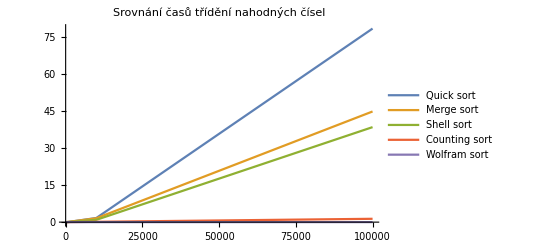

```mathematica
ListPlot[{
	{{10,quickSort10sr}, {100, quickSort100sr}, {1000, quickSort1000sr}, {10000, quickSort10000sr}, {100000, quickSort100000sr}},
	{{10,mergeSort10sr}, {100, mergeSort100sr}, {1000, mergeSort1000sr}, {10000, mergeSort10000sr}, {100000, mergeSort100000sr}},
	{{10,shellSort10sr}, {100, shellSort100sr}, {1000, shellSort1000sr}, {10000, shellSort10000sr}, {100000, shellSort100000sr}},
	{{10,countingSort10sr}, {100, countingSort100sr}, {1000, countingSort1000sr}, {10000, countingSort10000sr}, {100000, countingSort100000sr}},
	{{10,sort10sr}, {100, sort100sr}, {1000, sort1000sr}, {10000, sort10000sr}, {100000, sort100000sr}}
},
Joined->True,
PlotLegends->{"Quick sort", "Merge sort", "Shell sort", "Counting sort", "Wolfram sort"},
PlotLabel->"Srovnání časů třídění nahodných čísel",
PlotRange->All
]
```

```mathematica
Grid[{
{"n", "Quick sort", "Quick sort (T)", "Merge sort", "Merge sort (T)", "Shell sort", "Shell sort (T)", "Counting sort", "Counting sort (T)","Wolfram sort"},
{10, quickSort10sr, quickSort10Tsr,mergeSort10sr,mergeSort10Tsr,shellSort10sr,shellSort10Tsr,countingSort10sr,countingSort10Tsr,sort10sr},
{100, quickSort100sr, quickSort100Tsr,mergeSort100sr,mergeSort100Tsr,shellSort100sr,shellSort100Tsr,countingSort100sr,countingSort100Tsr,sort100sr},
{1000, quickSort1000sr, quickSort1000Tsr,mergeSort1000sr,mergeSort1000Tsr,shellSort1000sr,shellSort1000Tsr,countingSort1000sr,countingSort1000Tsr,sort1000sr},
{10000, quickSort10000sr, quickSort10000Tsr,mergeSort10000sr,mergeSort10000Tsr,shellSort10000sr,shellSort10000Tsr,countingSort10000sr,countingSort10000Tsr,sort10000sr},
{100000, quickSort100000sr, quickSort100000Tsr,mergeSort100000sr,mergeSort100000Tsr,shellSort100000sr,shellSort100000Tsr,countingSort100000sr,countingSort100000Tsr,sort100000sr}
}, Frame->All
]
```

n | Quick sort | Quick sort (T) | Merge sort | Merge sort (T) | Shell sort | Shell sort (T) | Counting sort | Counting sort (T) | Wolfram sort
10 | 0.000440945 | 0.000255759 | 0.00190007 | 0.000700066 | 0.000370382 | 0.000140961 | 0.003861 | 0.00682387 | 1.29091×10^-6
100 | 0.00589425 | 0.00511518 | 0.0147017 | 0.0140013 | 0.00361825 | 0.0030369 | 0.0039707 | 0.00782738 | 8.89091×10^-6
1000 | 0.0797329 | 0.0767277 | 0.11544 | 0.21002 | 0.0457579 | 0.0654281 | 0.0178625 | 0.0178625 | 0.0000289909
10000 | 1.67613 | 1.02304 | 1.57584 | 2.80026 | 0.940943 | 1.40961 | 0.132402 | 0.118214 | 0.000376636
100000 | 78.5215 | 12.7879 | 44.8883 | 35.0033 | 38.5389 | 30.369 | 1.35351 | 1.12172 | 0.0041262

## Závěr

V této úloze jsem provedl měření výpočetní složitosti třídících algoritmů. Vybral jsem si quick sort, merge sort, shell sort a counting sort. Ve všech měřeních byly výsledky podobné, nejpomalejší ze všech třídících algoritmů byl quick sort, Nejrychlejší z techo třídících algoritmů pak byl counting sort, tento algoritmus má lineární výpočetní složitost a proto dostahuje nejlepších výsledků. Vypočítané teoretické složitosti pro každý algoritmus ve většině případů odpovídali reálným naměřeným hodnotám. Ve všech případach byla nejrychlejší třídící funkce, ta která je součástí Woframu.

Mají nějakou výhodu algoritmy s časovou složitostí O(n^2) ? Proč se používají?
Jelikož tyto algoritmy mají časovou složitost n2, tak je není vhodné používat pro zpravovavani velkého množtví dat. Hlavní výhodou těchto algoritmů je jejich jednoduchost. Při malém množství zpracovávaných dat není veliký rozdíl v časově složitost oproti jiným rychlejším algoritmům.